```mathematica
x1=2+I;
y1=4I;
x2=-3;
y2=1-2I;
r1=1;
R1=1.5;
r2=2;
R2=1.5;
```

```mathematica
c1[t_]:=x1+Exp[2*Pi*I*t]*r1
C1[t_]:=y1+Exp[2*Pi*I*t]*R1
c2[t_]:=x2+Exp[2*Pi*I*t]*r2
C2[t_]:=y2+Exp[2*Pi*I*t]*R2
```

```mathematica
γ1[z_]:=r1*R1/(z-x1)+y1
γ1inv[z_]:=r1*R1/(z-y1)+x1
γ2[z_]:=r2*R2/(z-x2)+y2
γ2inv[z_]:=r2*R2/(z-y2)+x2
```

```mathematica
generators={γ1,γ1inv,γ2,γ2inv}
invInd={2,1,4,3}
NextOrder[{p_,restrictedGens_}]:=Module[
	{out={},i},
	For[i=1,i<=4,i++,
		If[Not[MemberQ[restrictedGens,i]],
			out=Append[out,{generators[[i]][p],{invInd[[i]]}}];
		]
	];
	out
]
NextOrderFromList[{old_,new_}]:=Module[
{out={},e},
Do[out=Join[out,NextOrder[e]],{e,new}];
{Join[old,Map[First,new]],out}
]
GetPoints[{old_,new_}]:=Join[old,Map[First,new]]
OrderN[{old_,new_},n_]:=If[n==0,GetPoints[{old,new}],OrderN[NextOrderFromList[{old,new}],n-1]]
```

{γ1,γ1inv,γ2,γ2inv}

{2,1,4,3}

```mathematica
g=generators
```

{γ1,γ1inv,γ2,γ2inv}

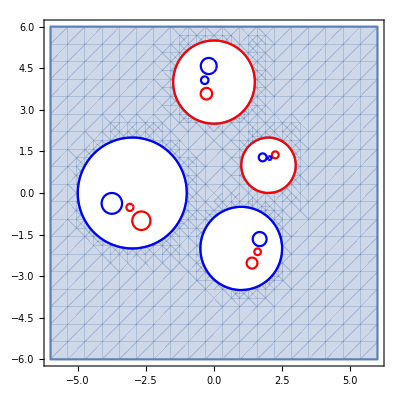

```mathematica
Show[
ComplexRegionPlot[{Abs[z-x1]>r1&&Abs[z-y1]>R1&&Abs[z-x2]>r2&&Abs[z-y2]>R2},{z,6}],
PP[1,c1,Red],
PP[2,c1,Red],
PP[3,c1,Red],
PP[4,c1,Red],
PP[1,C1,Red],
PP[2,C1,Red],
PP[3,C1,Red],
PP[4,C1,Red],
PP[1,c2,Blue],
PP[2,c2,Blue],
PP[3,c2,Blue],
PP[4,c2,Blue],
PP[1,C2,Blue],
PP[2,C2,Blue],
PP[3,C2,Blue],
PP[4,C2,Blue]
]
```

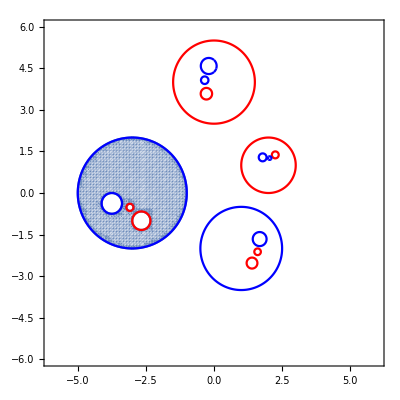

```mathematica
Show[
ComplexRegionPlot[{Abs[γ2[z]-x1]>r1&&Abs[γ2[z]-y1]>R1&&Abs[γ2[z]-x2]>r2&&Abs[γ2[z]-y2]>R2},{z,6},PlotPoints->100],
PP[1,c1,Red],
PP[2,c1,Red],
PP[3,c1,Red],
PP[4,c1,Red],
PP[1,C1,Red],
PP[2,C1,Red],
PP[3,C1,Red],
PP[4,C1,Red],
PP[1,c2,Blue],
PP[2,c2,Blue],
PP[3,c2,Blue],
PP[4,c2,Blue],
PP[1,C2,Blue],
PP[2,C2,Blue],
PP[3,C2,Blue],
PP[4,C2,Blue]
]
```